#### Coupling dispersion

```mathematica
ClearAll[κ,ω0,ω1,ω2,ω3,Ω]
Ω=({{ω1, -κ, 0}, {-κ, ω2, -κ}, {0, -κ, ω3}});
ωbAS=Eigenvalues[Ω][[3]];
ωbC=Eigenvalues[Ω][[2]];
ωbS=Eigenvalues[Ω][[1]];
```

```mathematica
rnum={ω1-> 1.0,ω2-> 1.0,ω3-> 1.0,κ-> 0.05};
```

```mathematica
Eigensystem[Ω]/.rnum//MatrixForm
```

(0.929289 | 1. | 1.07071
{1.,1.41421,1} | {-1.,1.26565×10^-13,1} | {1.,-1.41421,1})

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"Uncoupled frequency deviation (GHz)","Relative frequency (GHz)"}}];
```

```mathematica
rnum={ω1-> 1.0+δ,ω2-> 1.0,ω3-> 1.0,κ-> 0.05};
```

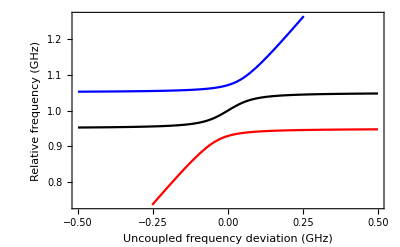

```mathematica
Plot[{ωbAS,ωbC,ωbS}/.rnum//Evaluate,{δ,-0.5,0.5},PlotStyle->{Blue,Black,Red}](*,{Gray,Dashed}}]*)
```

```mathematica
rnum={ω1-> ω0+D1 μ+D2/2 μ^2,ω2-> ω0+D1 μ+D2/2 μ^2,ω3-> ω0+D1 μ+D2/2 μ^2,κ->κ0 Exp[-α μ]};
```

```mathematica
DispModes = ({ωbAS,ωbC,ωbS}-ω0-D1 μ)/.rnum
```

{-D1 μ-ω0+Root[-16 D1 ⅇ^(-2 α μ) κ0^2 μ-8 D2 ⅇ^(-2 α μ) κ0^2 μ^2+8 D1^3 μ^3+12 D1^2 D2 μ^4+6 D1 D2^2 μ^5+D2^3 μ^6-16 ⅇ^(-2 α μ) κ0^2 ω0+24 D1^2 μ^2 ω0+24 D1 D2 μ^3 ω0+6 D2^2 μ^4 ω0+24 D1 μ ω0^2+12 D2 μ^2 ω0^2+8 ω0^3+(16 ⅇ^(-2 α μ) κ0^2-24 D1^2 μ^2-24 D1 D2 μ^3-6 D2^2 μ^4-48 D1 μ ω0-24 D2 μ^2 ω0-24 ω0^2) #1+(24 D1 μ+12 D2 μ^2+24 ω0) #1^2-8 #1^3&,3],-D1 μ-ω0+Root[-16 D1 ⅇ^(-2 α μ) κ0^2 μ-8 D2 ⅇ^(-2 α μ) κ0^2 μ^2+8 D1^3 μ^3+12 D1^2 D2 μ^4+6 D1 D2^2 μ^5+D2^3 μ^6-16 ⅇ^(-2 α μ) κ0^2 ω0+24 D1^2 μ^2 ω0+24 D1 D2 μ^3 ω0+6 D2^2 μ^4 ω0+24 D1 μ ω0^2+12 D2 μ^2 ω0^2+8 ω0^3+(16 ⅇ^(-2 α μ) κ0^2-24 D1^2 μ^2-24 D1 D2 μ^3-6 D2^2 μ^4-48 D1 μ ω0-24 D2 μ^2 ω0-24 ω0^2) #1+(24 D1 μ+12 D2 μ^2+24 ω0) #1^2-8 #1^3&,2],-D1 μ-ω0+Root[-16 D1 ⅇ^(-2 α μ) κ0^2 μ-8 D2 ⅇ^(-2 α μ) κ0^2 μ^2+8 D1^3 μ^3+12 D1^2 D2 μ^4+6 D1 D2^2 μ^5+D2^3 μ^6-16 ⅇ^(-2 α μ) κ0^2 ω0+24 D1^2 μ^2 ω0+24 D1 D2 μ^3 ω0+6 D2^2 μ^4 ω0+24 D1 μ ω0^2+12 D2 μ^2 ω0^2+8 ω0^3+(16 ⅇ^(-2 α μ) κ0^2-24 D1^2 μ^2-24 D1 D2 μ^3-6 D2^2 μ^4-48 D1 μ ω0-24 D2 μ^2 ω0-24 ω0^2) #1+(24 D1 μ+12 D2 μ^2+24 ω0) #1^2-8 #1^3&,1]}

```mathematica
plt1=Plot[DispModes/.{ω0->10,D1->1,D2-> -0.5,α->.1, κ0->.5}//Evaluate,{μ,-10,10},PlotStyle->{Blue,Black,Red},FrameLabel->{"μ","D_int(GHz)"}];
plt2=Plot[Abs[κ0 Exp[-α μ]]/.{ω0->10,D1->1,D2-> -0.5,α->.1, κ0->.5}//Evaluate,{μ,-10,10},PlotStyle->Black, FrameLabel->{"μ","κ(GHz)"}];
```

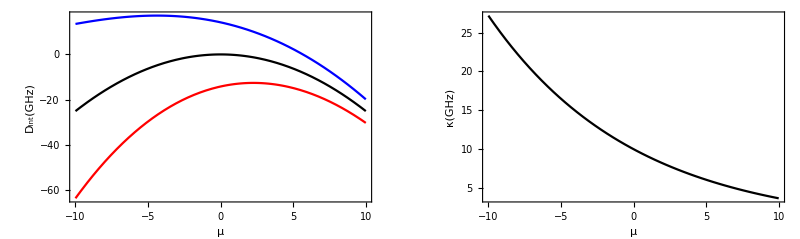

```mathematica
GraphicsGrid[{{plt1,plt2}}]
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\Mathematica\\CouplingDispersion.pdf",%]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\Papers\Journals\2024 - Nathalia - DOPO in photonic molecules\Figures\Mathematica\CouplingDispersion.pdf

#### Light distribution

```mathematica
ClearAll[κ,ω0,ω1,ω2,ω3,Ω]
Ω=({{ω1, -κ, 0}, {-κ, ω2, -κ}, {0, -κ, ω3}});
ωbAS=Eigenvalues[Ω][[3]];
ωbC=Eigenvalues[Ω][[2]];
ωbS=Eigenvalues[Ω][[1]];
```

```mathematica
aAS=Eigenvectors[Ω][[3]];
aC=Eigenvectors[Ω][[2]];
aS=Eigenvectors[Ω][[1]];
```

```mathematica
ωbC
```

Root[κ^2 ω1+κ^2 ω3-ω1 ω2 ω3+(-2 κ^2+ω1 ω2+ω1 ω3+ω2 ω3) #1+(-ω1-ω2-ω3) #1^2+#1^3&,2]

```mathematica
SetOptions[Plot,{Frame->True}];
```

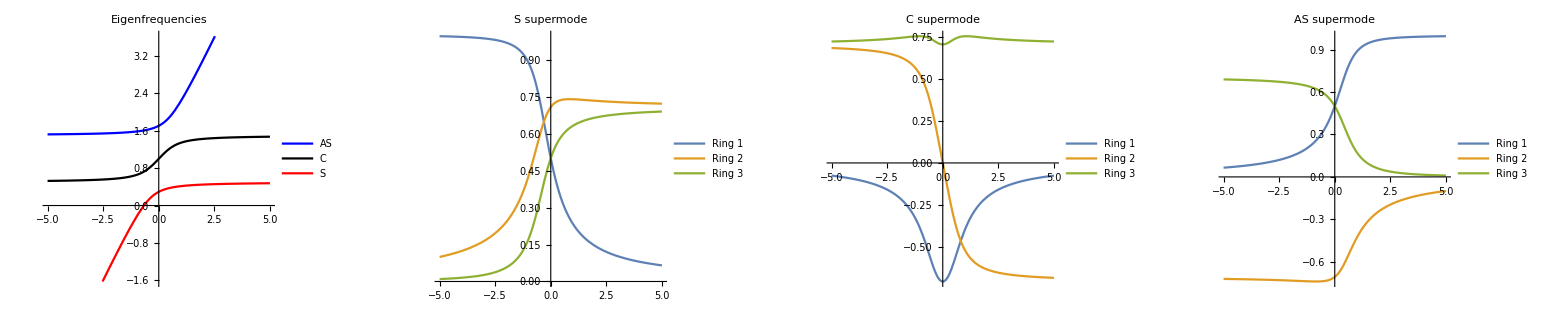

```mathematica
rnum={ω1-> 1.0+δ,ω2-> 1.0,ω3-> 1.0,κ-> .5};
plt0=Plot[{ωbAS,ωbC,ωbS}/.rnum//Evaluate,{δ,-5,5},PlotStyle->{Blue,Black,Red},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Supermode frequency, ω (GHz)"},PlotLabel->"Eigenfrequencies",PlotLegends->Placed[{"AS", "C", "S"},{0.75,0.2}]];
plt1=Plot[(aS/Norm[aS])/.rnum//Evaluate,{δ,-5,5},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Uncoupled rings amplitude"},PlotLabel->"S supermode",PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.25}]];
plt2=Plot[(aC/Norm[aC])/.rnum//Evaluate,{δ,-5,5},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Uncoupled rings amplitude"},PlotLabel->"C supermode",PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.25}]];
plt3=Plot[(aAS/Norm[aAS])/.rnum//Evaluate,{δ,-5,5},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Uncoupled rings amplitude"},PlotLabel->"AS supermode",PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.2}]];
Grid[{{plt0,plt1,plt2,plt3}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]
```

#### Light distribution

```mathematica
ClearAll[κ,ω0,ω1,ω2,ω3,Ω]
Ω=({{ω1, -κ}, {-κ, ω2}});
ωbAS=Eigenvalues[Ω][[2]];
ωbS=Eigenvalues[Ω][[1]];
```

```mathematica
aAS=Eigenvectors[Ω][[2]];
aS=Eigenvectors[Ω][[1]];
```

```mathematica
SetOptions[Plot,{Frame->True}];
```

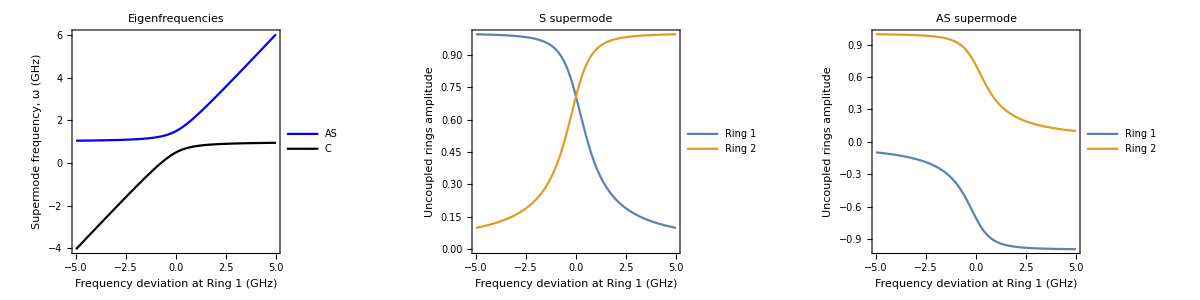

```mathematica
rnum={ω1-> 1.0+δ,ω2-> 1.0,ω3-> 1.0,κ-> 0.5};
plt0=Plot[{ωbAS,ωbS}/.rnum//Evaluate,{δ,-5,5},PlotStyle->{Blue,Black,Red},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Supermode frequency, ω (GHz)"},PlotLabel->"Eigenfrequencies",PlotLegends->Placed[{"AS", "C", "S"},{0.75,0.2}]];
plt1=Plot[(aS/Norm[aS])/.rnum//Evaluate,{δ,-5,5},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Uncoupled rings amplitude"},PlotLabel->"S supermode",PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.25}]];
plt2=Plot[(aAS/Norm[aAS])/.rnum//Evaluate,{δ,-5,5},FrameLabel->{"Frequency deviation at Ring 1 (GHz)","Uncoupled rings amplitude"},PlotLabel->"AS supermode",PlotLegends->Placed[{"Ring 1", "Ring 2", "Ring 3"},{0.75,0.2}]];
Grid[{{plt0,plt1,plt2}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]
```